```mathematica
nsol1 = NDSolve[
{-D[u[x,y], {x,2}]-D[u[x,y],{y,2}]==(x+y), u[x,0]==x, u[x,1]==0, u[0,y]==0, u[1,y]==1-y},
u[x,y],{x,0,1},{y,0,1}]
```

{{u[x,y]→InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>][x,y]}}

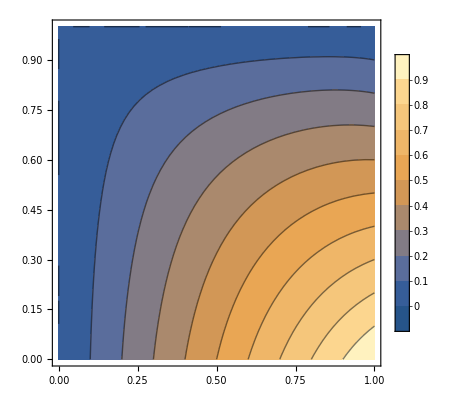

```mathematica
ContourPlot[Evaluate[u[x,y] /. nsol1],{x,0,1},{y,0,1},PlotLegends->Automatic]
```

```mathematica
nsol2 = NDSolve[
{D[u[x,y], {x,2}]+D[u[x,y],{y,2}]==3*x-6*y, u[x,0]==x, u[x,1]==1+x, u[0,y]==y, u[1,y]==1+y},
u[x,y],{x,0,1},{y,0,1}]
```

{{u[x,y]→InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>][x,y]}}

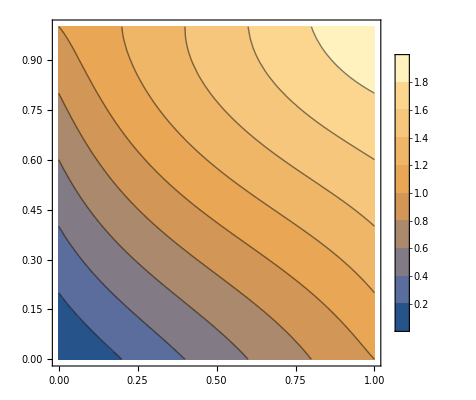

```mathematica
ContourPlot[Evaluate[u[x,y] /. nsol2],{x,0,1},{y,0,1},PlotLegends->Automatic]
```